Name : Agam Gupta
Secant Method

1.Perform 20iterations of the Secant  method to obtain the smallest positive root of the f(x)=Cos[x]in Interval [1,2] and take initial approximation x_0=1 and x_1=2

1 Iteration : 1.5649

Estimated error is : 0.435096

2 Iteration : 1.57098

Estimated error is : 0.0060742

3 Iteration : 1.5708

Estimated error is : 0.000182249

Return[1.5708]

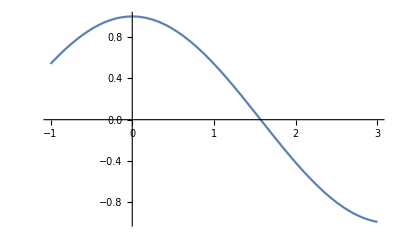

```mathematica
x0=1;
x1=2;
Nmax=20;
ϵ=0.000001;
f[x_]:=Cos[x];
If[N[f[x0]*f[x1]]>0,
Print[" These values do not satisfy the ivp,so change the values. "],
For[i=1,i≤Nmax,i++,
a=N[x1-f[x1]*(x1-x0)/(f[x1]-f[x0])];
If[Abs[x1-a]<ϵ,Return[a],x0=x1;x1=a];
Print[i," Iteration : ",a];
Print["Estimated error is : ",Abs[x1-x0]]]]
Plot[f[x],{x,-1,3}]
```

2).     Perform 20iterations of the Secant method to obtain the smallest positive root of the f(x)= x^3-2 x^2-3 x-1in Interval [1,2] and take initial approximation x_0=1 and x_1=2

1 iteration 1.1

Estimated error is: 0.9

2 iteration 1.15174

Estimated error is: 0.0517436

3 iteration 1.20345

Estimated error is: 0.0517062

4 iteration 1.19848

Estimated error is: 0.00496995

5 iteration 1.19869

Estimated error is: 0.000210411

Return[1.19869]

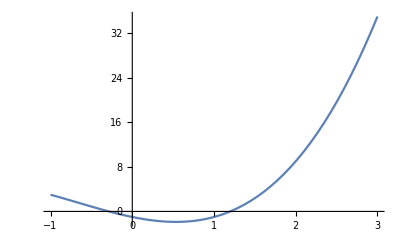

```mathematica
x0=1;
x1=2;
Nmax=20;
ϵ=0.000001;
f[x_]:=x^3+2 x^2-3x-1;
If[N[f[x0]*f[x1]]>0,
Print[" These values do not satisfy the ivp,so change the values. "],
For[i=1,i≤Nmax,i++,
a=N[x1-f[x1](x1-x0)/(f[x1]-f[x0])];
If[Abs[x1-a]<ϵ,Return[a],x0=x1;x1=a];
Print[i," iteration ",a];
Print["Estimated error is: ",Abs[x1-x0]]]]
Plot[f[x],{x,-1,3}]
```

3.Perform 3iterations of the Secant method to obtain the smallest positive root of the f(x)= x tan x+1in Interval [2.5,3] and take initial approximation x_0=2.5 and x_1=3

1 iteration 2.80125

Estimated error is: 0.198748

2 iteration 2.79843

Estimated error is: 0.00282467

3 iteration 2.79839

Estimated error is: 0.0000414676

Return[2.79839]

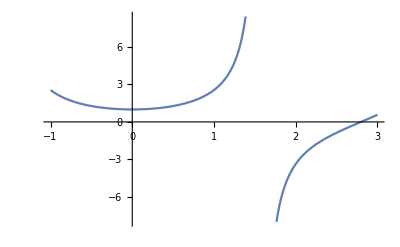

```mathematica
x0=2.5;
x1=3;
Nmax=4;
ϵ=0.000001;
f[x_]:=  x Tan[x]+1;
If[N[f[x0]*f[x1]]>0,
Print[" These values do not satisfy the ivp,so change the values. "],
For[i=1,i≤Nmax,i++,
a=N[x1-f[x1](x1-x0)/(f[x1]-f[x0])];
If[Abs[x1-a]<ϵ,Return[a],x0=x1;x1=a];
Print[i," iteration ",a];
Print["Estimated error is: ",Abs[x1-x0]]]]
Plot[f[x],{x,-1,3}]
```

4.PerForm 20iterations of the Secant method to obtain the smallest positive root of the          f(x)= x^3+5x+1in Interval [0,1] and take initial approximation x_0=0 and x_1=1

1 iteration 0.25

Estimated error is: 0.75

2 iteration 0.186441

Estimated error is: 0.0635593

3 iteration 0.201736

Estimated error is: 0.0152956

4 iteration 0.20164

Estimated error is: 0.0000964033

Return[0.20164]

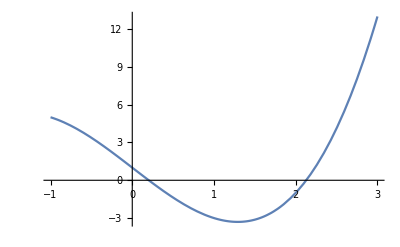

```mathematica
x0=0;
x1=1;
Nmax=20;
ϵ=0.000001;
f[x_]:=  x^3-5x+1;
If[N[f[x0]*f[x1]]>0,
Print[" These values do not satisfy the ivp,so change the values. "],
For[i=1,i≤Nmax,i++,
a=N[x1-f[x1](x1-x0)/(f[x1]-f[x0])];
If[Abs[x1-a]<ϵ,Return[a],x0=x1;x1=a];
Print[i," iteration ",a];
Print["Estimated error is: ",Abs[x1-x0]]]]
Plot[f[x],{x,-1,3}]
```

5.Perform 20iterations of the Secant method to obtain the smallest positive root of the f(x)=xe^x-cos x,   in Interval [0,1] and take initial approximation x_0=0 and x_1=1

1 iteration 0.314665

Estimated error is: 0.685335

2 iteration 0.446728

Estimated error is: 0.132063

3 iteration 0.531706

Estimated error is: 0.0849777

4 iteration 0.516904

Estimated error is: 0.0148014

5 iteration 0.517747

Estimated error is: 0.000842998

6 iteration 0.517757

Estimated error is: 9.90548×10^-6

Return[0.517757]

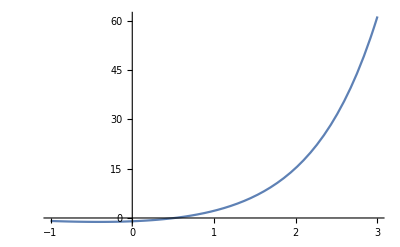

```mathematica
x0=0;
x1=1;
Nmax=20;
ϵ=0.000001;
f[x_]:=  x Exp[x]-Cos[x];
If[N[f[x0]*f[x1]]>0,
Print[" These values do not satisfy the ivp,so change the values. "],
For[i=1,i≤Nmax,i++,
a=N[x1-f[x1](x1-x0)/(f[x1]-f[x0])];
If[Abs[x1-a]<ϵ,Return[a],x0=x1;x1=a];
Print[i," iteration ",a];
Print["Estimated error is: ",Abs[x1-x0]]]]
Plot[f[x],{x,-1,3}]
```